```mathematica
Plot3D[x,{x,-1,1},{y,-1,1}]
```

-Graphics3D-

```mathematica
ParametricPlot[{t^2-1,2t},{t,-3,-3}]
```

ParametricPlot::plld: Endpoints for t in {t,-3,-3} must have distinct machine-precision numerical values.

General::stop: Further output of ParametricPlot::plld will be suppressed during this calculation.

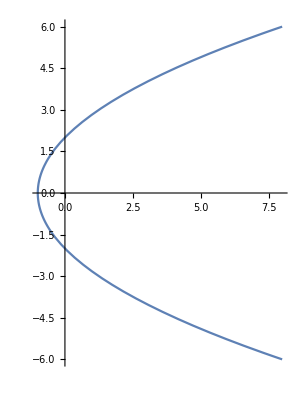

```mathematica
ParametricPlot[{t^2-1,2 t},{t,-3,3}]
```

```mathematica
Plot3D[1/(x + I y),{x,-5,5}.{y,-5,5}]
```

Plot3D::argrx: Plot3D called with 2 arguments; 3 arguments are expected.

```mathematica
Plot3D[Re[1/(x+ⅈ y)],{x,-5,5},{y,-5,5}]
```

-Graphics3D-

```mathematica
Plot3D[Im[1/(x+ⅈ y)],{x,-5,5},{y,-5,5}]
```

-Graphics3D-

```mathematica
Plot3D[Abs[1/(x+ⅈ y)],{x,-5,5},{y,-5,5}]
```

```mathematica
Plot3D[Arg[1/(x+ⅈ y)],{x,-5,5},{y,-5,5}]
```

-Graphics3D-

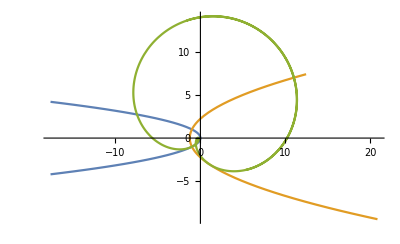

```mathematica
ParametricPlot[{{-t^2,t},{t^2-t-1,2t-1},{(2Cos[t]-1)^2-(2Sin[t]-1)^2-(2Cos[t]-1),2(2Cos[t]-1)(2Sin[t]-1)-(2Sin[t]-1)}},{t,-4.2,4.2}]
```

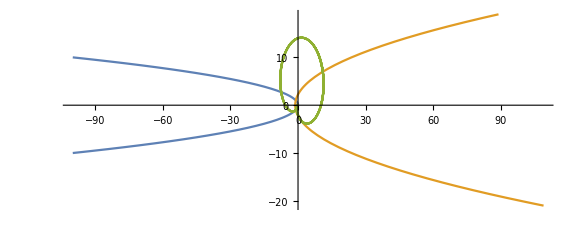

```mathematica
Show[%10,ImageSize->Large]
```

```mathematica
ParametricPlot3D[{r Cos[θ],r Sin[θ],3θ},{θ,0,6Pi},{r,0,10Pi}]
```

-Graphics3D-

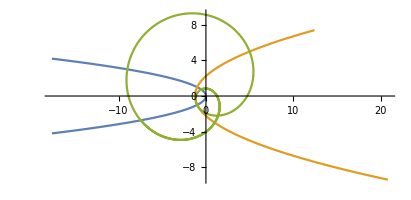

```mathematica
ParametricPlot[{{-t^2,t},{t^2-t-1,2t-1},{(2Cos[t]+1)^2-(2Sin[t]+1)^2-(2Cos[t]+1),2(2Cos[t]+1)(2Sin[t]+1)-(2Sin[t]+1)}},{t,-4.2,4.2}]
```

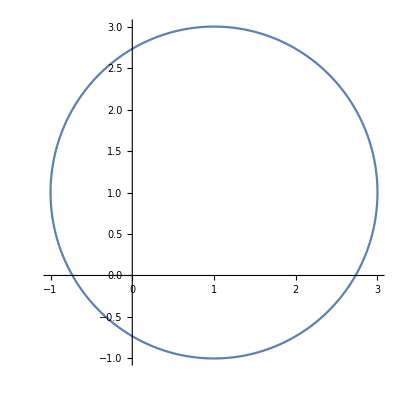

```mathematica
ParametricPlot[{2Cos[t]+1,2Sin[t]+1},{t,0,2Pi}]
```

```mathematica
ParametricPlot3D[{x,y,Abs[Sqrt[(x+I y)^-1]]},{x,-1,1},{y,-1,1}]
```

```mathematica
ParametricPlot3D[{x,y,Abs[1/((x+I y)^6-2)^2]},{x,-1.5,1.5},{y,-1.5,1.5}]
```

-Graphics3D-

```mathematica
Integrate[Log[Log[x]],x]
```

x Log[Log[x]]-LogIntegral[x]

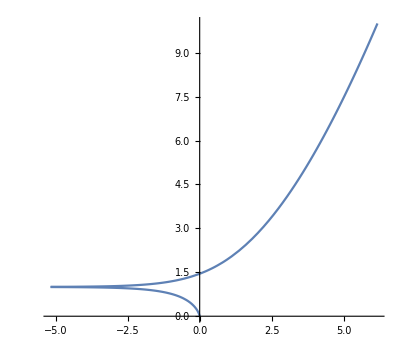

```mathematica
ParametricPlot[{LogIntegral[t],t},{t,0,10}]
```

```mathematica
ParametricPlot3D[{x,y,Abs[Cos[x+I y]]},{x,-5,5},{y,-1,1}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{x,y,Abs[Cos[x+ⅈ y]]},{x,-5,5},{y,-1,1},PlotStyle->RGBColor[0.17,1.,0.26]]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{x,y,Abs[Cos[x+ⅈ y]]},{x,-5,5},{y,-1,1},Mesh->None,PlotStyle->RGBColor[0.17,1.,0.26]]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{x,y,Abs[Cos[x+ⅈ y]]},{x,-5,5},{y,-1,1},Mesh->Automatic,MeshFunctions->{#3&},Mesh->None,PlotStyle->RGBColor[0.17,1.,0.26]]
```

-Graphics3D-

```mathematica
ParametricPlot3D[{x,y,0.1Cos[(x*y)/2]*Abs[x+I y]},{x,-2Pi,2Pi},{y,-2Pi,2Pi}]
```

-Graphics3D-